```mathematica
sim=Block[{i,data={},name0="Sim",name1=".csv"},For[i=1,i<=23,i++,AppendTo[data,Import["~/Work/ElektroShag/Data/Simul/"<>name0<>ToString[i]<>name1,"Table","FieldSeparators"->";"]]];data];
```

```mathematica
sim=Block[{i,data={},name0="Sim",name1=".csv"},For[i=1,i<=23,i++,AppendTo[data,Import["~/Work/ElektroShag/Data/Simul/"<>name0<>ToString[i]<>name1,"Table","FieldSeparators"->";"]]];data];
```

```mathematica
Table[Block[{data=sim[[1]][[2;;]][[All,2;;]][[All,i]],avr},avr=Mean[data[[10;;40]]];data-avr],{j,1,Length@
```

{50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0004,50.0004,50.0004,50.0004,50.0004,50.0004,50.0005,50.0005,50.0005,50.0005,50.0005,50.0006,50.0006,50.0006,50.0006,50.0006,50.0007,50.0007,50.0007,50.0007,50.0007,50.0008,50.0008,50.0008,50.0008,50.0008,50.0009,50.0009,50.0009,50.0009,50.001,50.001,50.001,50.001,50.0011,50.0011,50.0011,50.0011,50.0012,50.0012,50.0012,50.0012,50.0013,50.0013,50.0013,50.0013,50.0014,50.0014,50.0014,50.0014,50.0015,50.0015,50.0015,50.0015,50.0016,50.0016,50.0016,50.0016,50.0017,50.0017,50.0017,50.0017,50.0018,50.0018,50.0018,50.0019,50.0019,50.0019,50.0019,50.002,50.002,50.002,50.0021,50.0021,50.0021,50.0021,50.0022,50.0022,50.0022,50.0023,50.0023,50.0023,50.0024,50.0024,50.0024,50.0024,50.0025,50.0025,50.0025,50.0026,50.0026,50.0026,50.0027,50.0027,50.0027,50.0028,50.0028,50.0028,50.0028,50.0029,50.0029,50.0029,50.003,50.003,50.003,50.0031,50.0031,50.0031,50.0032,50.0032,50.0032,50.0032,50.0033,50.0033,50.0033,50.0034,50.0034,50.0034,50.0035,50.0035,50.0035,50.0035,50.0036,50.0036,50.0036,50.0037,50.0037,50.0037,50.0037,50.0038,50.0038,50.0038,50.0039,50.0039,50.0039,50.0039,50.004,50.004,50.004,50.0041,50.0041,50.0041,50.0041,50.0042,50.0042,50.0042,50.0042,50.0042,50.0043,50.0043,50.0043,50.0043,50.0044,50.0044,50.0044,50.0044,50.0045,50.0045,50.0045,50.0045,50.0046,50.0046,50.0046,50.0046,50.0046,50.0047,50.0047,50.0047,50.0047,50.0047,50.0048,50.0048,50.0048,50.0048,50.0048,50.0049,50.0049,50.0049,50.0049,50.0049,50.005,50.005,50.005,50.005,50.0051,50.0051,50.0051,50.0051,50.0051,50.0052,50.0052,50.0052,50.0052,50.0052,50.0053,50.0053,50.0053,50.0053,50.0053,50.0054,50.0054,50.0054,50.0054,50.0055,50.0055,50.0055,50.0055,50.0056,50.0056,50.0056,50.0056,50.0056,50.0057,50.0057,50.0057,50.0057,50.0058,50.0058,50.0058,50.0058,50.0059,50.0059,50.0059,50.0059,50.006,50.006,50.006,50.006,50.0061,50.0061,50.0061,50.0062,50.0062,50.0062,50.0062,50.0063,50.0063,50.0063,50.0064,50.0064,50.0064,50.0065,50.0065,50.0065,50.0065,50.0066,50.0066,50.0066,50.0067,50.0067,50.0068,50.0068,50.0068,50.0069,50.0069,50.0069,50.007,50.007,50.007,50.0071,50.0071,50.0071,50.0072,50.0072,50.0073,50.0073,50.0073,50.0074,50.0074,50.0074,50.0075,50.0075,50.0075,50.0076,50.0076,50.0076,50.0077,50.0077,50.0078,50.0078,50.0078,50.0079,50.0079,50.0079,50.008,50.008,50.008,50.0081,50.0081,50.0081,50.0082,50.0082,50.0082,50.0083,50.0083,50.0083,50.0084,50.0084,50.0084,50.0085,50.0085,50.0086,50.0086,50.0086,50.0087,50.0087,50.0087,50.0088,50.0088,50.0088,50.0089,50.0089,50.0089,50.009,50.009,50.0091,50.0091,50.0091,50.0092,50.0092,50.0093,50.0093,50.0093,50.0094,50.0094,50.0094,50.0095,50.0095,50.0096,50.0096,50.0096,50.0097,50.0097,50.0098,50.0098,50.0098,50.0099,50.0099,50.0099,50.01,50.01,50.01,50.0101,50.0101,50.0101,50.0101,50.0101,50.0102,50.0102,50.0102,50.0101,50.0101,50.0101,50.0101,50.0101,50.01,50.01,50.01,50.0099,50.0099,50.0098,50.0098,50.0098,50.0097,50.0097,50.0096,50.0096,50.0096,50.0095,50.0095,50.0095,50.0094,50.0094,50.0094,50.0094,50.0093,50.0093,50.0093,50.0093,50.0093,50.0093,50.0092,50.0092,50.0092,50.0092,50.0092,50.0092,50.0092,50.0092,50.0092,50.0093,50.0093,50.0093,50.0093,50.0093,50.0093,50.0094,50.0094,50.0094,50.0094,50.0095,50.0095,50.0095,50.0095,50.0096,50.0096,50.0096,50.0096,50.0096,50.0097,50.0097,50.0097,50.0097,50.0097,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0094,50.0094,50.0094,50.0094,50.0094,50.0094,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0096,50.0096,50.0096,50.0096,50.0096,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0094,50.0094,50.0094,50.0094,50.0094,50.0094,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0095,50.0096,50.0096,50.0096,50.0096,50.0096,50.0096,50.0097,50.0097,50.0097,50.0097,50.0097,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.01,50.01,50.01,50.01,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0099,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0098,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0097,50.0012,49.9965,49.9937,49.9917,49.9902,49.989,49.988,49.9873,49.9869,49.9868,49.987,49.9874,49.9881,49.989,49.9901,49.9914,49.9928,49.9942,49.9957,49.9972,49.9986,50.,50.0013,50.0024,50.0035,50.0045,50.0053,50.0059,50.0064,50.0066,50.0067,50.0067,50.0065,50.0062,50.0058,50.0052,50.0046,50.0039,50.0031,50.0023,50.0015,50.0006,49.9997,49.9989,49.998,49.9972,49.9965,49.9957,49.9951,49.9945,49.994,49.9935,49.9931,49.9928,49.9925,49.9923,49.9922,49.9921,49.9921,49.9922,49.9923,49.9925,49.9927,49.9929,49.9932,49.9935,49.9939,49.9943,49.9947,49.9951,49.9955,49.996,49.9964,49.9968,49.9973,49.9978,49.9982,49.9986,49.999,49.9993,49.9997,50.0001,50.0005,50.0008,50.0011,50.0013,50.0016,50.0018,50.0021,50.0023,50.0025,50.0027,50.0028,50.003,50.0032,50.0033,50.0035,50.0036,50.0037,50.0038,50.004,50.0041,50.0042,50.0043,50.0044,50.0046,50.0047,50.0049,50.0049,50.0051,50.0052,50.0054,50.0055,50.0056,50.0057,50.0059,50.0061,50.0062,50.0063,50.0064,50.0065,50.0067,50.0067,50.0068,50.0069,50.0071,50.0072,50.0072,50.0073,50.0075,50.0076,50.0076,50.0077,50.0078,50.0079,50.0079,50.0079,50.008,50.0081,50.0081,50.0081,50.008,50.0081,50.0081,50.008,50.0079,50.0078,50.0077,50.0076,50.0074,50.0073,50.0072,50.007,50.0068,50.0067,50.0065,50.0063,50.0061,50.006,50.0058,50.0056,50.0054,50.0053,50.0051,50.0049,50.0048,50.0047,50.0045,50.0043,50.0042,50.0041,50.004,50.0038,50.0037,50.0036,50.0034,50.0032,50.0031,50.0028,50.0026,50.0025,50.0022,50.0019,50.0017,50.0015,50.0011,50.0008,50.0005,50.0002,49.9998,49.9995,49.9992,49.9987,49.9984,49.998,49.9976,49.9972,49.997,49.9966,49.9962,49.9959,49.9956,49.9952,49.995,49.9948,49.9945,49.9943,49.9941,49.9938,49.9937,49.9936,49.9934,49.9932,49.9932,49.993,49.9929,49.9929,49.9928,49.9927,49.9927,49.9926,49.9925,49.9925,49.9924,49.9923,49.9923,49.9922,49.9921,49.992,49.9919,49.9917,49.9917,49.9915,49.9914,49.9913,49.9911,49.9909,49.9908,49.9906,49.9904,49.9903,49.9901,49.99,49.9898,49.9896,49.9895,49.9894,49.9892,49.9892,49.989,49.9889,49.9889,49.9888,49.9887,49.9888,49.9887,49.9887,49.9888,49.9887,49.9888,49.9889,49.9889,49.9891,49.9891,49.9892,49.9894,49.9895,49.9897,49.9898,49.9899,49.9901,49.9903,49.9904,49.9906,49.9907,49.9909,49.9911,49.9911,49.9913,49.9914,49.9915,49.9917,49.9917,49.9918,49.9919,49.9919,49.9921,49.9921,49.9921,49.9922,49.9921,49.9922,49.9921,49.9921,49.9921,49.992,49.992,49.992,49.9918,49.9918,49.9917,49.9916,49.9916,49.9914,49.9914,49.9913,49.9912,49.9912,49.991,49.9911,49.9909,49.9909,49.9909,49.9907,49.9908,49.9907,49.9907,49.9907,49.9906,49.9907,49.9907,49.9906,49.9907,49.9907,49.9908,49.9907,49.9908,49.9908,49.9908,49.9909,49.9909,49.9909,49.991,49.9909,49.991,49.991,49.991,49.9911,49.991,49.9911,49.991,49.9911,49.991,49.991,49.9911,49.991,49.9911,49.991,49.991,49.991,49.9909,49.991,49.9908,49.9909,49.9908,49.9908,49.9908,49.9907,49.9907,49.9906,49.9906,49.9906,49.9905,49.9905,49.9904,49.9905,49.9904,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9901,49.9901,49.99,49.9901,49.99,49.9901,49.99,49.99,49.9901,49.99,49.9901,49.99,49.99,49.99,49.99,49.9901,49.99,49.9901,49.99,49.99,49.99,49.99,49.9901,49.99,49.9901,49.99,49.9901,49.9901,49.99,49.9901,49.9901,49.9902,49.9901,49.9902,49.9901,49.9901,49.9902,49.9902,49.9903,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9905,49.9904,49.9905,49.9906,49.9905,49.9906,49.9906,49.9907,49.9907,49.9907,49.9907,49.9907,49.9908,49.9908,49.9909,49.9908,49.9909,49.9909,49.9909,49.9909,49.9908,49.9909,49.9909,49.9909,49.9909,49.9908,49.9909,49.9908,49.9909,49.9907,49.9908,49.9907,49.9907,49.9907,49.9906,49.9907,49.9906,49.9906,49.9905,49.9905,49.9905,49.9904,49.9905,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9901,49.9901,49.99,49.9901,49.99,49.99,49.99,49.99,49.99,49.9899,49.99,49.9899,49.99,49.99,49.9899,49.99,49.9899,49.99,49.99,49.99,49.9901,49.9901,49.9902,49.9901,49.9902,49.9902,49.9903,49.9903,49.9903,49.9904,49.9904,49.9905,49.9905,49.9905,49.9906,49.9905,49.9907,49.9906,49.9907,49.9907,49.9907,49.9908,49.9907,49.9908,49.9907,49.9907,49.9908,49.9907,49.9908,49.9907,49.9908,49.9907,49.9907,49.9908,49.9907,49.9907,49.9906,49.9906,49.9906,49.9905,49.9906,49.9905,49.9905,49.9905,49.9904,49.9904,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9901,49.9901,49.9901,49.99,49.99,49.99,49.99,49.99,49.9899,49.99,49.99,49.9899,49.99,49.9899,49.99,49.99,49.99,49.9901,49.99,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9903,49.9903,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9906,49.9905,49.9906,49.9906,49.9907,49.9907,49.9907,49.9908,49.9908,49.9907,49.9908,49.9908,49.9908,49.9908,49.9907,49.9908,49.9908,49.9907,49.9908,49.9907,49.9907,49.9907,49.9906,49.9906,49.9907,49.9905,49.9906,49.9906,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9902,49.9902,49.9903,49.9902,49.9902,49.9903,49.9902,49.9902,49.9902,49.9903,49.9902,49.9902,49.9903,49.9902,49.9902,49.9903,49.9902,49.9902,49.9902,49.9903,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9904,49.9905,49.9906,49.9905,49.9905,49.9906,49.9906,49.9905,49.9905,49.9906,49.9906,49.9905,49.9905,49.9906,49.9905,49.9905,49.9904,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.99,49.99,49.99,49.99,49.99,49.9899,49.99,49.99,49.99,49.9899,49.9899,49.99,49.99,49.9901,49.99,49.99,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9904,49.9903,49.9903,49.9904,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9906,49.9906,49.9906,49.9905,49.9905,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9905,49.9905,49.9905,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9906,49.9906,49.9906,49.9906,49.9905,49.9905,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.99,49.99,49.99,49.99,49.99,49.99,49.99,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9906,49.9905,49.9905,49.9905,49.9905,49.9904,49.9905,49.9905,49.9904,49.9904,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9904,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9904,49.9905,49.9905,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9904,49.9905,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9902,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9902,49.9902,49.9902,49.9901,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9904,49.9904,49.9905,49.9904,49.9904,49.9905,49.9905,49.9904,49.9905,49.9905,49.9904,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9907,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9905,49.9905,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9901,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9904,49.9904,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9905,49.9905,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9906,49.9905,49.9905,49.9905,49.9904,49.9905,49.9904,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9901,49.9902,49.9901,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9906,49.9905,49.9906,49.9906,49.9906,49.9906,49.9907,49.9906,49.9906,49.9907,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9905,49.9905,49.9905,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9904,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9902,49.9903,49.9902,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9904,49.9905,49.9904,49.9905,49.9905,49.9905,49.9905,49.9904,49.9905,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.99,49.99,49.9901,49.99,49.99,49.99,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9905,49.9905,49.9905,49.9905,49.9905,49.9905,49.9906,49.9905,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9906,49.9905,49.9906,49.9905,49.9905,49.9905,49.9905,49.9905,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9902,49.9902,49.9901,49.9901,49.9901,49.9901,49.9901,49.99,49.9901,49.99,49.99,49.9901,49.99,49.9901,49.9901,49.9901,49.9901,49.9902,49.9902,49.9902,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9904,49.9903,49.9904,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9903,49.9902,49.9903,49.9902,49.9903,49.9902,49.9903,49.9902,49.9903,49.9902,49.9903,49.9902,49.9903}

```mathematica
timeToVal[data_]:=DateList[data][[-1]]
```

```mathematica
Table[Length@sim[[i]],{i,Length@sim}]
```

{2501,2501,2501,2502,2502,2502,2502,2502,2502,2502,2502,2502,2502,2501,2501,2501,2501,2501,2501,2501,2501,2501,2501}

```mathematica
nodesN=Flatten[StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,1]],"N"],1];
```

```mathematica
tipesofdata={"f","r","u","i","P","Q","au","ai"};
```

```mathematica
datatypes=Table[Flatten[Position[Flatten[StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],DigitCharacter]],tipesofdata[[i]]]],{i,Length@tipesofdata}];
```

```mathematica
moci=Block[{data=Transpose[sim[[1]][[2;;]][[All,datatypes[[5]]+1]]]}
```

704.528

```mathematica
StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],LetterCharacter]
```

{{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{6},{6},{6},{},{1},{2},{3},{4},{5},{6},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{},{1},{2},{3},{4},{5},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{5},{5},{5},{6},{6},{6},{},{1},{2},{3},{4},{5},{6},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{2},{2},{2},{3},{3},{3},{4},{4},{4},{},{1},{2},{3},{4},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{2},{2},{2},{},{1},{2},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{},{1},{},{},{},{1},{1},{1},{},{1}}

```mathematica
Table[Mean[[[i]][[;;100]]],{i,1,Length@
```

{50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0001,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0002,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0003,50.0004,50.0004,50.0004,50.0004,50.0004,50.0004,50.0005,50.0005,50.0005,50.0005,50.0005,50.0006,50.0006,50.0006,50.0006,50.0006,50.0007,50.0007,50.0007,50.0007,50.0007,50.0008,50.0008,50.0008,50.0008,50.0008,50.0009,50.0009,50.0009,50.0009,50.001,50.001,50.001,50.001,50.0011,50.0011,50.0011,50.0011,50.0012,50.0012,50.0012,50.0012,50.0013,50.0013,50.0013,50.0013,50.0014,50.0014,50.0014,50.0014,50.0015,50.0015,50.0015}

```mathematica
Table[Transpose[sim[[i]][[2;;]][[All,datatypes[[1]]+1]]]
```

```mathematica
Manipulate[ListPlot[Transpose[sim[[i]][[2;;]][[All,datatypes[[1]]+1]]],PlotRange->All],{i,1,Length@sim,1}]
```

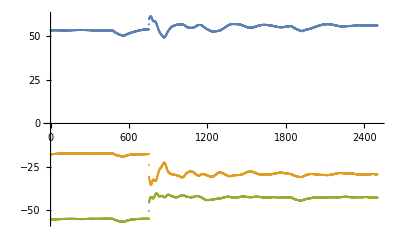

```mathematica
ListPlot[Transpose[sim[[16]][[2;;]][[All,(datatypes[[6]]+1)[[;;3]]]]],PlotRange->All]
```

```mathematica
Table[
```

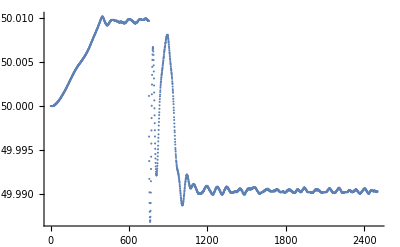

```mathematica
ListPlot[sim[[1]][[All,2]]]
```

```mathematica
sim[[1]][[1]]
```

{Time,N1_f,N1_r,N1_u,N1_i1,N1_P1,N1_Q1,N1_i2,N1_P2,N1_Q2,N1_i3,N1_P3,N1_Q3,N1_i4,N1_P4,N1_Q4,N1_au,N1_ai1,N1_ai2,N1_ai3,N1_ai4,N2_f,N2_r,N2_u,N2_i1,N2_P1,N2_Q1,N2_i2,N2_P2,N2_Q2,N2_i3,N2_P3,N2_Q3,N2_i4,N2_P4,N2_Q4,N2_i5,N2_P5,N2_Q5,N2_i6,N2_P6,N2_Q6,N2_au,N2_ai1,N2_ai2,N2_ai3,N2_ai4,N2_ai5,N2_ai6,N3_f,N3_r,N3_u,N3_i1,N3_P1,N3_Q1,N3_i2,N3_P2,N3_Q2,N3_i3,N3_P3,N3_Q3,N3_i4,N3_P4,N3_Q4,N3_au,N3_ai1,N3_ai2,N3_ai3,N3_ai4,N4_f,N4_r,N4_u,N4_i1,N4_P1,N4_Q1,N4_i2,N4_P2,N4_Q2,N4_i3,N4_P3,N4_Q3,N4_i4,N4_P4,N4_Q4,N4_i5,N4_P5,N4_Q5,N4_au,N4_ai1,N4_ai2,N4_ai3,N4_ai4,N4_ai5,N5_f,N5_r,N5_u,N5_i1,N5_P1,N5_Q1,N5_au,N5_ai1,N6_f,N6_r,N6_u,N6_i1,N6_P1,N6_Q1,N6_i2,N6_P2,N6_Q2,N6_i3,N6_P3,N6_Q3,N6_i4,N6_P4,N6_Q4,N6_i5,N6_P5,N6_Q5,N6_i6,N6_P6,N6_Q6,N6_au,N6_ai1,N6_ai2,N6_ai3,N6_ai4,N6_ai5,N6_ai6,N7_f,N7_r,N7_u,N7_i1,N7_P1,N7_Q1,N7_i2,N7_P2,N7_Q2,N7_i3,N7_P3,N7_Q3,N7_i4,N7_P4,N7_Q4,N7_au,N7_ai1,N7_ai2,N7_ai3,N7_ai4,N8_f,N8_r,N8_u,N8_i1,N8_P1,N8_Q1,N8_i2,N8_P2,N8_Q2,N8_au,N8_ai1,N8_ai2,N9_f,N9_r,N9_u,N9_i1,N9_P1,N9_Q1,N9_au,N9_ai1,N10_f,N10_r,N10_u,N10_i1,N10_P1,N10_Q1,N10_i2,N10_P2,N10_Q2,N10_i3,N10_P3,N10_Q3,N10_i4,N10_P4,N10_Q4,N10_au,N10_ai1,N10_ai2,N10_ai3,N10_ai4,N11_f,N11_r,N11_u,N11_i1,N11_P1,N11_Q1,N11_i2,N11_P2,N11_Q2,N11_au,N11_ai1,N11_ai2,N12_f,N12_r,N12_u,N12_i1,N12_P1,N12_Q1,N12_i2,N12_P2,N12_Q2,N12_au,N12_ai1,N12_ai2,N13_f,N13_r,N13_u,N13_i1,N13_P1,N13_Q1,N13_au,N13_ai1,N14_f,N14_r,N14_u,N14_i1,N14_P1,N14_Q1,N14_au,N14_ai1,N15_f,N15_r,N15_u,N15_i1,N15_P1,N15_Q1,N15_au,N15_ai1}

```mathematica
Transpose[sim[[16]][[2;;]][[All,(datatypes[[6]]+1)[[1]]]]]
```

Transpose::nmtx: The first two levels of {53.5011,53.5031,53.5081,53.512,53.5176,53.5232,53.5289,53.5347,53.5405,53.5463,53.5521,53.5578,53.5634,53.5688,53.5739,53.5788,53.5833,53.5875,53.5913,53.5947,53.5978,53.6004,53.6027,53.6046,53.6062,53.6076,53.6086,53.6094,53.61,53.6104,53.6105,53.6106,53.6104,53.6101,53.6097,53.6091,53.6084,53.6076,53.6065,53.6054,53.6041,53.6026,53.601,53.5992,53.5974,53.5954,53.5932,53.591,53.5886,53.5862,«2450»} cannot be transposed.

```mathematica
Machi
```